```mathematica
(* Functions *)
(*Lindblad[QMC0_,H0_,Llist0_,rhocq0_]:=Module[{QMC1=QMC0,H1=H0,Llist1=Llist0,rhocq1=rhocq0},
M1=-I KroneckerProduct[H1,IdentityMatrix[QMC1[Num]*HilbertD]]+I KroneckerProduct[IdentityMatrix[QMC1[Num]*HilbertD],Transpose[H1]] +Sum[KroneckerProduct[L,Conjugate[L]]-1/2KroneckerProduct[ConjugateTranspose[L].L,IdentityMatrix[HilbertD*QMC1[Num]]]-1/2KroneckerProduct[IdentityMatrix[HilbertD*QMC1[Num]],Transpose[L].Conjugate[L]],{L,Llist1}];
rhovec=L2V[QMC1,rhocq1];
rhovect=V2L[QMC1,MatrixFunction[Exp,M1*t].rhovec]
(*rhovect=V2L[QMC1,Power[M1,t1].rhovec]*)
]
Phi[rhot0_,infI0_,supI0_,s0_,QMC0_]:=Module[{rhot1=rhot0,infI1=infI0,supI1=supI0,s1=s0,QMC1=QMC0},
PS=KroneckerProduct[Transpose[States2Bra[QMC1,s1]].States2Bra[QMC1,s1],IdentityMatrix[HilbertD]];
(Tr[PS.rhot1]-infI1)(Tr[PS.rhot1]-supI1)
]*)
(* loop *)
Isolate[Phi0_,l0_,u0_]:=Module[{Phi1=Phi0,l1=l0,u1=u0,PhiDer,LST,ResLST,l2,u2,M,MM,Delta,c,LH,RH},
PhiDer=D[Phi1, t];
LST=List[];
ResLST=List[];
AppendTo[LST,{l1,u1}];
While[Length[LST]>0,
(*Print[LST];*)
l2=LST[[1]][[1]];
u2=LST[[1]][[2]];
LST=Delete[LST,1];
M=Ceiling[N[Max[Abs[MaxValue[#,{t}∈Interval[{l2,u2}]]&/@PhiDer],Abs[MinValue[#,{t}∈Interval[{l2,u2}]]&/@PhiDer]]*100]]/100;
MM=Ceiling[N[Max[Abs[MaxValue[#,{t}∈Interval[{l2,u2}]]&/@D[PhiDer, t]],Abs[MinValue[#,{t}∈Interval[{l2,u2}]]&/@D[PhiDer, t]]]*100]]/100;
Delta=(u2-l2)/2;
c=(l2+u2)/2;
LH=0;
RH=0;
If[Abs[N[Phi1/.t->l2]]>M*Delta || Abs[N[Phi1/.t->c]]>M*Delta,
LH=LH+1;];
If[Abs[N[Phi1/.t->u2]]>M*Delta || Abs[N[Phi1/.t->c]]>M*Delta,
RH=RH+1;];
If[Abs[N[PhiDer/.t->l2]]>MM*Delta || Abs[N[PhiDer/.t->c]]>MM*Delta,
If[N[(Phi1/.t->l2)]* N[(Phi1/.t->c)]<=0,
AppendTo[ResLST,{l2,c}];];
LH=LH+1;];
If[Abs[N[PhiDer/.t->u2]]>MM*Delta || Abs[N[PhiDer/.t->c]]>MM*Delta,
If[N[(Phi1/.t->u2)]*N[(Phi1/.t->c)]<=0,
AppendTo[ResLST,{c,u2}];];
RH=RH+1;];
If[LH==0,AppendTo[LST,{l2,c}];];
If[RH==0,AppendTo[LST,{c,u2}];];
];
ResLST
]
Refinement[Phi0_,IsoLST0_,Aug0_]:=Module[{Phi1=Phi0,IsoLST1=IsoLST0,Aug1=Aug0,NewLST,ZeroLST,l,r,c,len},
NewLST=List[];
ZeroLST=List[];
Do[
l=i[[1]];r=i[[2]];
len=r-l;
While[len>Aug1,
c=(l+r)/2;
If[(Phi1/.t->l)*(Phi1/.t->c)<0,
r=c;,
l=c;
];
len=len/2;
];
AppendTo[NewLST,{l,r}];
,{i,IsoLST1}];

Do[
AppendTo[ZeroLST,(i[[1]]+i[[2]])/2];
,{i,NewLST}];
ZeroLST=Sort[ZeroLST]
]
SatInterval[Phi0_,l0_,r0_,Aug0_]:=Module[{Phi1=Phi0,l1=l0,r1=r0,Aug1=Aug0,IsoLST,RefLST,ZeroLST,SatLST,l},
IsoLST=Isolate[Phi1,l1,r1];
Print[IsoLST];
ZeroLST=Refinement[Phi1,IsoLST,Aug1];
SatLST=List[];
l=l1;
Do[
If[N[Phi1/.t->(l+i)/2]>0,AppendTo[SatLST,{l,i,4}];];
l=i;
,{i,ZeroLST}];
If[N[Phi1/.t->(l+r1)/2]>0,AppendTo[SatLST,{l,r1,4}]];
N[SatLST]
]
PostOrder[tree0_]:=Module[{tree1=tree0,S1,cur,ResLST},
S1=CreateDataStructure["Stack"];
ResLST=List[];
S1["Push",tree1];
While[!S1["EmptyQ"],
cur=S1["Pop"];
AppendTo[ResLST,cur["Data"]];
If[!cur["Left"]["NullQ"],S1["Push",cur["Left"]];];
If[!cur["Right"]["NullQ"],S1["Push",cur["Right"]]];
];
Reverse[ResLST]
]
```

```mathematica
(* Interval *)
Interval2Expr[Interval0_,var0_]:=Module[{Interval1=Interval0,var1=var0,min,max,type,Flag,expr,exprLST},
Flag=False;
Do[
min=i[[1]];
max=i[[2]];type=i[[3]];
If[type==1,expr=min<var1<max];
If[type==2,expr=min≤var1<max];
If[type==3,expr=min<var1≤max];
If[type==4,expr=min≤var1≤max];
If[!Flag,exprLST=expr,exprLST=exprLST||expr];
Flag=True;
,{i,Interval1}];
exprLST
]
Expr2Interval[exprlst0_]:=Module[{exprlst1=exprlst0,expr,min,max,type,Len,InterLST},
InterLST=List[];
If[exprlst1[[0]]=== Or,
Len=Length[exprlst1],
Len=1;exprlst1={exprlst1}];
Do[
expr=exprlst1[[i]];
If[Length[expr]==2,min=expr[[2]];max=expr[[2]];type=4];
If[Length[expr]==3,
If[expr[[0]]===LessEqual,min=expr[[1]];max=expr[[3]];type=4];
If[expr[[0]]===Less,min=expr[[1]];max=expr[[3]];type=1];
];
If[Length[expr]==5,
min=expr[[1]];
max=expr[[5]];
If[expr[[2]]===Less&&expr[[4]]===Less,type=1];
If[expr[[2]]===LessEqual&&expr[[4]]===Less,type=2];
If[expr[[2]]===Less&&expr[[4]]===LessEqual,type=3];
If[expr[[2]]===LessEqual&&expr[[4]]===LessEqual,type=4];
];
AppendTo[InterLST,{min,max,type}];
,{i,Len}];
InterLST
]
InterValIntersection[int10_,int20_]:=Module[{int1=int10,int2=int20,int3,exprlst1,exprlst2,exprlst3},
exprlst1=Interval2Expr[int1,x];
exprlst2=Interval2Expr[int2,x];
exprlst3=Reduce[(exprlst1)&&(exprlst2)];
If[!Head[exprlst3]===Symbol,int3=Expr2Interval[exprlst3],int3={{1,0,1}}]
]
InterValUnion[int10_,int20_]:=Module[{int1=int10,int2=int20,int3,exprlst1,exprlst2,exprlst3},
exprlst1=Interval2Expr[int1,x];
exprlst2=Interval2Expr[int2,x];
exprlst3=Reduce[(exprlst1)||(exprlst2)];
If[!Head[exprlst3]===Symbol,int3=Expr2Interval[exprlst3],int3={{1,0,1}}]
]
InterValComple[Comple0_,int0_]:=Module[{Comple1=Comple0,int1=int0,int3,exprlst1,exprlst2,exprlst3},
exprlst1=Interval2Expr[Comple1,x];
exprlst2=Interval2Expr[int1,x];
exprlst3=Reduce[(exprlst1)&&(!(exprlst2))];
If[!Head[exprlst3]===Symbol,int3=Expr2Interval[exprlst3],int3={{1,0,1}}]
]
IntervalUntil[J10_,J20_,I0_]:=Module[{J1=J10,J2=J20,I1=I0,Res,ResLST,expr1,expr2,expr3,expr4},
ResLST={{0,0,1}};
Do[Do[
Clear[t1];
Clear[t2];
expr1=Interval2Expr[{j1},t1];
expr2=Interval2Expr[I1,t2];
expr3=t1+t2≤j1[[2]];
expr4=Interval2Expr[{j2},t1+t2];
Res=Reduce[Exists[t2,expr1&&expr2&&expr3&&expr4],t1];
If[!Head[Res]===Symbol,Res=Expr2Interval[Res],Res={{1,0,1}}];
ResLST=InterValUnion[ResLST,Res];
,{j2,J2}];
,{j1,J1}];
ResLST
]
```

```mathematica
ValTree[ds0_,B0_]:=Module[{ds1=ds0,B1=B0,val,S,J1,J2,ele,Flag,LST,Inter,F,Res,infI,supI,typeI,infF,supF,typeF,infG,supG,typeG,H,G,I1},
S=CreateDataStructure["Stack"];
(* Solution exists or not *)
Flag=True;
LST=PostOrder[ds1];
Do[
If[!(StringQ[i]||(ListQ[i]&&StringQ[i[[1]]])),
S["Push",i];
,
If[i=="wedge",
J1=S["Pop"];
J2=S["Pop"];
Inter=InterValIntersection[J1,J2];
If[!Head@Inter===Symbol,
S["Push",Inter];,
Flag=False;
Break[];];
];
If[i=="not",
ele=S["Pop"];
ele=InterValComple[{{0,B1,4}},ele];
S["Push",ele]];
If[ListQ[i],
infI=i[[2]][[1]][[1]];
supI=i[[2]][[1]][[2]];
typeI=i[[2]][[1]][[3]];
I1={{infI,supI,typeI}};
J2=S["Pop"];
J1=S["Pop"];
Res=IntervalUntil[J1,J2,I1];
S["Push",Res];
];
];
,{i,LST}];
If[Flag,res=S["Pop"],Flag]
]
```

```mathematica
(* Initializtion *)
Hadmard = {{1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],-1/Sqrt[2]}};
PLUS=1/Sqrt[2]{{1,1}};MINUS=1/Sqrt[2]{{1,-1}};ZERO={{1,0}};ONE={{0,1}};
X={{0,1},{1,0}};
Y={{0,-I},{I,0}};
F=ZERO;S=ONE;
```

```mathematica
HZero=ZeroMatrix[4*2];
L1=KroneckerProduct[Transpose[Num2Bra[4,3]].Num2Bra[4,1],Transpose[F].PLUS];L2=KroneckerProduct[Transpose[Num2Bra[4,2]].Num2Bra[4,1],Transpose[S].MINUS];L3=KroneckerProduct[Transpose[Num2Bra[4,1]].Num2Bra[4,2],Transpose[S].MINUS];L4=KroneckerProduct[Transpose[Num2Bra[4,4]].Num2Bra[4,2],Transpose[F].PLUS];L5=KroneckerProduct[Transpose[Num2Bra[4,1]].Num2Bra[4,3],Transpose[F].PLUS];L6=KroneckerProduct[Transpose[Num2Bra[4,4]].Num2Bra[4,3],Transpose[S].MINUS];
```

```mathematica
QW=QCTMCintialize[4,2,{"s0","s1","s2","s3"},HZero,{L1,L2,L3,L4,L5,L6}];
```

```mathematica
Clear[t];
```

```mathematica
M=GovernMat2[QW];
```

```mathematica
rho01=KroneckerProduct[Transpose[Num2Bra[4,1]].Num2Bra[4,1],1/2*IdentityMatrix[2]];
rho02=KroneckerProduct[Transpose[Num2Bra[4,1]].Num2Bra[4,1],Transpose[ZERO].ZERO];
rho03=KroneckerProduct[Transpose[Num2Bra[4,1]].Num2Bra[4,1],Transpose[PLUS].PLUS];
```

```mathematica
Frhot=V2L[QW,MatrixExp[M*t].L2V[QW,rho01]];
```

```mathematica
Frhot
```

{{1/8 ⅇ^-t (-2+ⅇ^(t+1/2 (-2-√2) t)+ⅇ^(t+1/2 (-2+√2) t))+1/8 ⅇ^-t (2+ⅇ^(t+1/2 (-2-√2) t)+ⅇ^(t+1/2 (-2+√2) t)),0,0,0,0,0,0,0},{0,1/8 ⅇ^-t (-2+ⅇ^(t+1/2 (-2-√2) t)+ⅇ^(t+1/2 (-2+√2) t))+1/8 ⅇ^-t (2+ⅇ^(t+1/2 (-2-√2) t)+ⅇ^(t+1/2 (-2+√2) t)),0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,-((2+√2) (ⅇ^(1/2 (-2-√2) t)-ⅇ^(1/2 (-2+√2) t)))/(4 (1+√2)),0,0,0,0},{0,0,0,0,-((2+√2) (ⅇ^(1/2 (-2-√2) t)-ⅇ^(1/2 (-2+√2) t)))/(4 (1+√2)),0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-(-2-2 √2-ⅇ^(1/2 (-2-√2) t)+3 ⅇ^(1/2 (-2+√2) t)+2 √2 ⅇ^(1/2 (-2+√2) t))/(4 (1+√2)),0},{0,0,0,0,0,0,0,-(-2-2 √2-ⅇ^(1/2 (-2-√2) t)+3 ⅇ^(1/2 (-2+√2) t)+2 √2 ⅇ^(1/2 (-2+√2) t))/(4 (1+√2))}}

```mathematica
rho1=Limit[Frhot,t->Infinity]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1/2,0},{0,0,0,0,0,0,0,1/2}}

```mathematica
ProjS0=KroneckerProduct[Transpose[Num2Bra[4,1]].Num2Bra[4,1],IdentityMatrix[2]];
ProjS1=KroneckerProduct[Transpose[Num2Bra[4,2]].Num2Bra[4,2],IdentityMatrix[2]];
ProjS2=KroneckerProduct[Transpose[Num2Bra[4,3]].Num2Bra[4,3],IdentityMatrix[2]];
ProjS3=KroneckerProduct[Transpose[Num2Bra[4,4]].Num2Bra[4,4],IdentityMatrix[2]];
```

```mathematica
X0t=Tr[Frhot.ProjS0];
X1t=Simplify[Tr[Frhot.(ProjS1+ProjS2)]]
X2t=Simplify[Tr[Frhot.ProjS3]]
```

(ⅇ^(-1/2 (2+√2) t) (-1+ⅇ^(√2 t)))/(√2)

1/2 (-1+√2) (2 (1+√2)-(3+2 √2) ⅇ^(1/2 (-2+√2) t)+ⅇ^(-1/2 (2+√2) t))

```mathematica
X00t=Simplify[Tr[Frhot.ProjS0]]
X01t=Simplify[Tr[Frhot.ProjS1]]
X10t=Simplify[Tr[Frhot.ProjS2]]
X11t=Simplify[Tr[Frhot.ProjS3]]
```

1/2 ⅇ^(-1/2 (2+√2) t) (1+ⅇ^(√2 t))

(ⅇ^(-1/2 (2+√2) t) (-1+ⅇ^(√2 t)))/(2 √2)

(ⅇ^(-1/2 (2+√2) t) (-1+ⅇ^(√2 t)))/(2 √2)

1/2 (-1+√2) (2 (1+√2)-(3+2 √2) ⅇ^(1/2 (-2+√2) t)+ⅇ^(-1/2 (2+√2) t))

```mathematica
(* Path Formula *)
Phi1=X1t-1/5;
Phi2=X2t-X1t;
B=25;
```

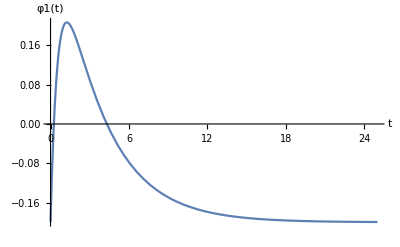

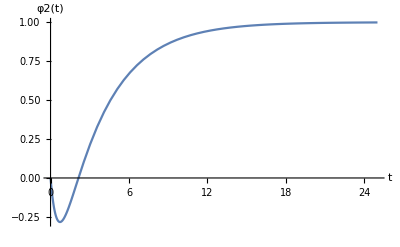

```mathematica
Phi1Plot=Plot[Phi1,{t,1/1000,25},AxesLabel->{"t","φ1(t)"}]
Phi2Plot=Plot[Phi2,{t,0,25},AxesLabel->{"t","φ2(t)"}]
```

```mathematica
Export[NotebookDirectory[]<>"Phi1Plot.eps",Phi1Plot];
Export[NotebookDirectory[]<>"Phi2Plot.eps",Phi2Plot];
```

```mathematica
(* Satisfied Interval *)
Inter1=SatInterval[Phi1,0,11,1/10000]
Inter2=SatInterval[Phi2,1/1000,11,1/1000]
```

{{0,11/32},{33/8,143/32}}

{{0.257267,4.30388,4.}}

{{33013/16000,3081/1280}}

{{2.13615,11.,4.}}

```mathematica
tree= CreateDataStructure["BinaryTree","not"->{{"U",{{0,20,4}}}->{{{0,B,4}},"wedge"->{Inter1,"not"->{{"U",{{0,5,4}}}->{{{0,B,4}},Inter2},Null}}},Null}];
```

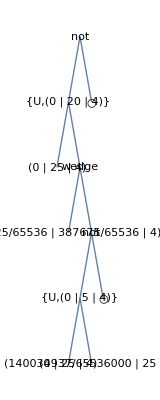

General::munfl: -3.99404×10^-284 1.03401×10^-28 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -3.99404×10^-284 (-1.41736×10^-47) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -3.99404×10^-284 (-3.56356×10^-48) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Inverse::sing: Matrix {{-0.397052,0.,-4.72519×10^-17,-0.105238,-1.63523×10^-15,0.0149099,2.08701,-2.84515,-2.77277,-242.881,1.42937,2.6884×10^31,-3.44543×10^31,-4.11195×10^31,-8.42819×10^15,7.16308,-2.26917,-5.48225,-50.6104,«13»,-0.0460824,-0.00657365,-4.77008×10^-18,6.59195×10^-17,1.73472×10^-16,-3.82859×10^-19,5.65305×10^-33,0.,0.,0.,0.,0.,0.,-5.51061×10^-34,0.,0.,0.,0.,«14»},«50»} is singular.

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

```mathematica
tree["Visualization"]
```